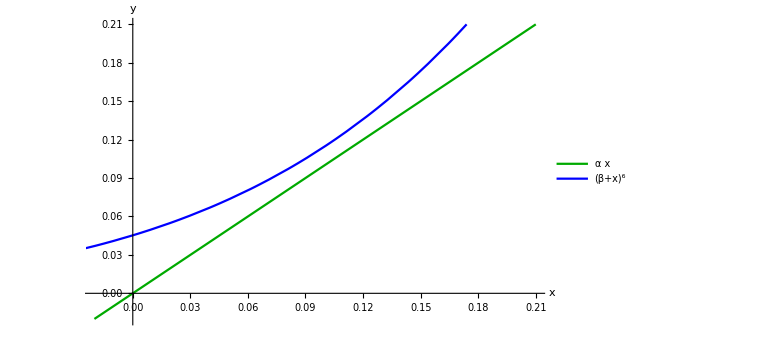

```mathematica
a=1;
b=0.597;
f[a_, x_]=a*x;
g[b_, x_]=(b+x)^6;
answer ={x, f[a,x]}/. Solve[f[a,x]==g[b,x], x,Reals];
fg=Plot[
{f[a,x], g[b, x]}, 
{x, -1, 1}, 
PlotLegends->{α*x, (β+x)^6},
PlotRange->{{-0.02, 0.21}, {-0.02, 0.21}},
PlotStyle->{Darker[Green], Blue},
ImageSize->Large,
(*Epilog->{Red,PointSize[Large], Point[answer]},*)
AxesLabel->{Style["x", Bold,20],Style["y",Bold,20]},
TicksStyle->Directive[FontSize->16]
]
Export["C:\\Users\\user\\Desktop\\a.svg", fg];
(*Export["C:\\Users\\user\\Desktop\\big.svg",fg,ImageSize->2000,"CompressionLevel"->0];*)
```